# Introgression and hybridization

## 2 Locus Models

## KJB model

#### Update of reference after transmission

```mathematica
npi=si/(1+pi si)pi(1-pi)+pi//FullSimplify
npj=si/(1+pi si)Dij+pj//FullSimplify
nDij=(Dij+si/(1+pi si)(1-2pi)Dij)(1-rij)-(1-rij)(pi-npi)(pj-npj)//FullSimplify
```

(pi (1+si))/(1+pi si)

pj+(Dij si)/(1+pi si)

-(Dij (-1+rij) (1+si))/(1+pi si)^2

```mathematica
Clear[Itterate2locus]
Itterate2locus[t_,pi0_,si0_,sj0_,rij0_]:=Itterate2locus[t,pi0,si0,sj0,rij0]=Block[
{pi,pj,Dij,si,sj,rij},
Itterate2locus[0,pi0,si0,sj0,rij0]={pi0,pi0,pi0(1-pi0)};

si=si0;
sj=sj0;
rij=rij0;
pi=Itterate2locus[t-1,pi0,si0,sj0,rij0][[1]];
pj=Itterate2locus[t-1,pi0,si0,sj0,rij0][[2]];
Dij=Itterate2locus[t-1,pi0,si0,sj0,rij0][[3]];

{npi,npj,nDij}
]
```

#### Update of reference after selection

```mathematica
npi=si/(1+pi si)pi(1-pi)+pi//FullSimplify
npj=si/(1+pi si)Dij+pj//FullSimplify
nDij=(1-rij)((Dij+si/(1+pi si)(1-2pi)Dij)-(pi-npi)(pj-npj))//FullSimplify
```

(pi (1+si))/(1+pi si)

pj+(Dij si)/(1+pi si)

-(Dij (-1+rij) (1+si))/(1+pi si)^2

## Haploid selection

#### Selection

```mathematica
FAB1=FAB(1+s)/WBAR;
FAb1=FAb(1+s)/WBAR;
FaB1=FaB 1/WBAR;
Fab1=Fab 1/WBAR;
```

```mathematica
WBAR=(1+s)FAB+(1+s)FAb+FaB+Fab;
```

```mathematica
FAB1+FAb1+FaB1+Fab1//FullSimplify
```

1

#### Reproduction

```mathematica
FAB2=FAB1(FAB1+FAb1/2+FaB1/2+Fab1(1-r)/2)+FAb1(FAB1/2+FaB1 r/2)+FaB1(FAB1/2+r/2 FAb1)+Fab1(FAB1(1-r)/2);
FAb2=FAB1(FAb1/2+Fab1(r/2))+FAb1(FAB1/2+FAb1+FaB1(1-r)/2+Fab1/2)+FaB1(FAb1(1-r)/2)+Fab1(FAB1(r/2)+FAb1/2);
FaB2=FAB1(FaB1/2+Fab1(r/2))+FAb1(FaB1(1-r)/2)+FaB1(FAB1/2+FAb1(1-r)/2+FaB1+Fab1/2)+Fab1(FAB1 r/2+FaB1/2);
Fab2=FAB1(Fab1(1-r)/2)+FAb1(FaB1(r/2)+Fab1/2)+FaB1(FAb1 r/2+Fab1/2)+Fab1(FAB1(1-r)/2+FAb1/2+FaB1/2+Fab1);
```

```mathematica
FAB2+FAb2+FaB2+Fab2//FullSimplify
```

1

#### Convert metrics in KJB:

```mathematica
FA2=FAB2+FAb2;
FB2=FAB2+FaB2;
Fa2=FaB2+Fab2;
Fb2=FAb2+Fab2;
```

```mathematica
FA2/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FA (1+s))/(1+FA s)

```mathematica
FB2/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FB+DAB s+FA FB s)/(1+FA s)

These are the same equations as KJB 2 locus model.

```mathematica
CovAB=(FAB2-FA2 FB2 )/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

-(DAB (-1+r) (1+s))/(1+FA s)^2

This one is not the same as equations from KJB 2 locus model. But see below:

```mathematica
Solve[(DAB+s/(1+FA s)(1-2FA)DAB)(1-r)+a==-(DAB (-1+r) (1+s))/(1+FA s)^2,a]
```

{{a→-(DAB (-1+r) (-FA s^2+FA^2 s^2))/(1+FA s)^2}}

```mathematica
Solve[A(FA-(FA (1+s))/(1+FA s))(FB-(FB+DAB s+FA FB s)/(1+FA s))==-(DAB (-1+r) (-FA s^2+FA^2 s^2))/(1+FA s)^2,A]//FullSimplify
```

{{A→-1+r}}

The update of reference should be: -(1-r) (pi-npi)(pj-npj)

#### KJB after selection only:

```mathematica
FA1=FAB1+FAb1;
FB1=FAB1+FaB1;
Fa1=FaB1+Fab1;
Fb1=FAb1+Fab1;
```

```mathematica
FA1/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FA (1+s))/(1+FA s)

```mathematica
FB1/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FB+DAB s+FA FB s)/(1+FA s)

```mathematica
CovAB=(FAB1-FA1 FB1 )/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(DAB (1+s))/(1+FA s)^2

This is the KJB model after selection but without update of reference.

```mathematica
DAB1=(DAB+s/(1+FA s)(1-2FA)DAB)//FullSimplify
```

(DAB (1+s-FA s))/(1+FA s)

Solve for what the update of reference should be to make the models match.

```mathematica
Solve[(DAB (1+s-FA s))/(1+FA s)+a==(DAB (1+s))/(1+FA s)^2,a]//FullSimplify
```

{{a→(DAB (-1+FA) FA s^2)/(1+FA s)^2}}

This should be the update of reference.

```mathematica
Solve[A(FA-(FA (1+s))/(1+FA s))(FB-(FB+DAB s+FA FB s)/(1+FA s))==(DAB (-1+FA) FA s^2)/(1+FA s)^2,A]//FullSimplify
```

{{A→-1}}

### JMS hitchhiking model:

This is the same as the JMS hitchhiking model where we have locus i and j, with frequency pi and pj respectively. We solve for the change of variables between the models :

```mathematica
Solve[{pi Q==pi pj+Dij,pi(1-Q)==pi(1-pj)-Dij,(1-pi)R==(1-pi) pj-Dij,(1-pi)(1-R)==(1-pi)(1-pj)+Dij},{Dij,pj}]//Simplify
```

{{Dij→-(-1+pi) pi (Q-R),pj→pi (Q-R)+R}}

```mathematica
Q1=((1+pi s)Q+r(1-pi)(R-Q))/(1+pi s);
R1=((1+pi s)R+r(1+s)pi(Q-R))/(1+pi s);
pi1=pi(1+s)/(1+pi s);
```

```mathematica
Dij1=(1-pi1)pi1(Q1-R1)//FullSimplify
```

((-1+pi) pi (-1+r) (Q-R) (1+s))/(1+pi s)^2

This is the covariance between locus i and j in the next generation if we follow the JMS model for hitchhiking. It is analogous to the 2 locus haploid selection model and the diploid multiplicative selection model.

```mathematica
-(Dij (-1+r) (1+s))/(1+pi s)^2
```

-(Dij (-1+r) (1+s))/(1+pi s)^2

## Diploid multiplicative selection

#### Selection

```mathematica
WABAB=(1+s)(1+s);
WABAb=(1+s)(1+s);
WABaB=(1+s);
WABab=(1+s);
WAbAb=(1+s)(1+s);
WAbaB=(1+s);
WAbab=(1+s);
WaBaB=1;
WaBab=1;
Wabab=1;
```

```mathematica
WBAR = FAB FAB WABAB+2FAB FAb WABAb+2FAB FaB WABaB+2FAB Fab WABab+FAb FAb WAbAb+2FAb FaB WAbaB +2FAb Fab WAbab+FaB FaB WaBaB+2FaB Fab WaBab+Fab Fab Wabab;
```

```mathematica
WBAR//FullSimplify
```

(Fab+FaB+(FAb+FAB) (1+s))^2

```mathematica
FABAB=(FAB^2 WABAB)/WBAR;
FABAb=2FAB FAb WABAb/WBAR;
FABaB=2FAB FaB WABaB/WBAR;
FABab=2FAB Fab WABab/WBAR;
FAbAb=FAb^2 WAbAb/WBAR;
FAbaB=2FAb FaB WAbaB/WBAR;
FAbab=2FAb Fab WAbab/WBAR;
FaBaB=FaB^2 WaBaB/WBAR;
FaBab=2FaB Fab WaBab/WBAR;
Fabab=Fab^2 Wabab/WBAR;
```

```mathematica
FABAB+FABAb+FABaB+FABab+FAbAb+FAbaB+FAbab+FaBaB+FaBab+Fabab//FullSimplify
```

1

Which is the same as haploid selection if you express as haplotypes:

```mathematica
FAB1=(FAB (1+s))/(Fab+FaB+(FAb+FAB) (1+s));
FAb1=(FAb (1+s))/(Fab+FaB+(FAb+FAB) (1+s));
FaB1=FaB/(Fab+FaB+(FAb+FAB) (1+s));
Fab1=Fab/(Fab+FaB+(FAb+FAB) (1+s));
```

```mathematica
FAB1+FAb1+FaB1+Fab1//FullSimplify
```

1

#### Reproduction (gamete formation)

```mathematica
FAB2=FAB1(FAB1+FAb1/2+FaB1/2+Fab1(1-r)/2)+FAb1(FAB1/2+FaB1 r/2)+FaB1(FAB1/2+r/2 FAb1)+Fab1(FAB1(1-r)/2);
FAb2=FAB1(FAb1/2+Fab1(r/2))+FAb1(FAB1/2+FAb1+FaB1(1-r)/2+Fab1/2)+FaB1(FAb1(1-r)/2)+Fab1(FAB1(r/2)+FAb1/2);
FaB2=FAB1(FaB1/2+Fab1(r/2))+FAb1(FaB1(1-r)/2)+FaB1(FAB1/2+FAb1(1-r)/2+FaB1+Fab1/2)+Fab1(FAB1 r/2+FaB1/2);
Fab2=FAB1(Fab1(1-r)/2)+FAb1(FaB1(r/2)+Fab1/2)+FaB1(FAb1 r/2+Fab1/2)+Fab1(FAB1(1-r)/2+FAb1/2+FaB1/2+Fab1);
```

```mathematica
(FAB2+FAb2+FaB2+Fab2)//Simplify
```

1

#### Metrics

```mathematica
FA2=FAB2+FAb2;
FB2=FAB2+FaB2;
Fa2=FaB2+Fab2;
Fb2=FAb2+Fab2;
```

```mathematica
FA2/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FA (1+s))/(1+FA s)

```mathematica
FB2/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FB+DAB s+FA FB s)/(1+FA s)

These are the same equations as KJB 2 locus model.

```mathematica
CovAB=(FAB2-FA2 FB2 )/.Fab->1-FaB-FAb-FAB/.FAb->PA-FAB/.FaB->PB-FAB/.FAB->DAB+PA PB//FullSimplify
```

-(DAB (-1+r) (1+s))/(1+PA s)^2

The covariance in the next generation is the same as under a haploid selection model as under a diploid multiplicative selection model.

The effect of selection on building up linkage in the next generation:

```mathematica
Manipulate[Plot[{( 1+s)/(1+PA s)^2,1},{PA,0,1},PlotRange->{Automatic,{0,2}}],{s,0,1}]
```

## Diploid additive selection

#### Selection

```mathematica
WABAB=(1+s+s);
WABAb=(1+s+s);
WABaB=(1+s);
WABab=(1+s);
WAbAb=(1+s+s);
WAbaB=(1+s);
WAbab=(1+s);
WaBaB=1;
WaBab=1;
Wabab=1;
```

```mathematica
WBAR = FAB FAB WABAB+2FAB FAb WABAb+2FAB FaB WABaB+2FAB Fab WABab+FAb FAb WAbAb+2FAb FaB WAbaB +2FAb Fab WAbab+FaB FaB WaBaB+2FaB Fab WaBab+Fab Fab Wabab;
```

```mathematica
WBAR//FullSimplify
```

(Fab+FaB+FAb+FAB) (Fab+FaB+FAb+FAB+2 (FAb+FAB) s)

```mathematica
FABAB=(FAB^2 WABAB)/WBAR;
FABAb=2FAB FAb WABAb/WBAR;
FABaB=2FAB FaB WABaB/WBAR;
FABab=2FAB Fab WABab/WBAR;
FAbAb=FAb^2 WAbAb/WBAR;
FAbaB=2FAb FaB WAbaB/WBAR;
FAbab=2FAb Fab WAbab/WBAR;
FaBaB=FaB^2 WaBaB/WBAR;
FaBab=2FaB Fab WaBab/WBAR;
Fabab=Fab^2 Wabab/WBAR;
```

```mathematica
FABAB+FABAb+FABaB+FABab+FAbAb+FAbaB+FAbab+FaBaB+FaBab+Fabab//FullSimplify
```

1

Which is the same as haploid selection if you express as haplotypes:

```mathematica
FAB1=(2FABAB+FABAb+FABaB+FABab)/2//FullSimplify;
FAb1=(FABAb+2FAbAb+FAbaB+FAbab)/2//FullSimplify;
FaB1=(FABaB+FAbaB+2FaBaB+FaBab)/2//FullSimplify;
Fab1=(FABab+FAbab+FaBab+2Fabab)/2//FullSimplify;
```

```mathematica
FAB1=FAB(Fab+FaB+FAb+FAB+(Fab+FaB+2 (FAb+FAB)) s)/WBAR;
```

```mathematica
FAb1=FAb(Fab+FaB+FAb+FAB+(Fab+FaB+2 (FAb+FAB)) s)/WBAR;
```

```mathematica
FaB1=FaB(Fab+FaB+(FAb+FAB) (1+s))/WBAR;
```

```mathematica
Fab1=Fab(Fab+FaB+(FAb+FAB) (1+s))/WBAR;
```

```mathematica
FAB1+FAb1+FaB1+Fab1//FullSimplify
```

1

#### Reproduction (gamete formation)

```mathematica
FAB2=FAB1(FAB1+FAb1/2+FaB1/2+Fab1(1-r)/2)+FAb1(FAB1/2+FaB1 r/2)+FaB1(FAB1/2+r/2 FAb1)+Fab1(FAB1(1-r)/2);
FAb2=FAB1(FAb1/2+Fab1(r/2))+FAb1(FAB1/2+FAb1+FaB1(1-r)/2+Fab1/2)+FaB1(FAb1(1-r)/2)+Fab1(FAB1(r/2)+FAb1/2);
FaB2=FAB1(FaB1/2+Fab1(r/2))+FAb1(FaB1(1-r)/2)+FaB1(FAB1/2+FAb1(1-r)/2+FaB1+Fab1/2)+Fab1(FAB1 r/2+FaB1/2);
Fab2=FAB1(Fab1(1-r)/2)+FAb1(FaB1(r/2)+Fab1/2)+FaB1(FAb1 r/2+Fab1/2)+Fab1(FAB1(1-r)/2+FAb1/2+FaB1/2+Fab1);
```

```mathematica
(FAB2+FAb2+FaB2+Fab2)//Simplify
```

1

#### Metrics

```mathematica
FA2=FAB2+FAb2;
FB2=FAB2+FaB2;
Fa2=FaB2+Fab2;
Fb2=FAb2+Fab2;
```

```mathematica
FA2/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FA (1+s+FA s))/(1+2 FA s)

```mathematica
FB2/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

(FB+DAB s+2 FA FB s)/(1+2 FA s)

These are NOT the same equations as KJB 2 locus model.

```mathematica
CovAB=(FAB2-FA2 FB2 )/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

-(DAB (-1+r) (1+FA s) (1+s+FA s))/(1+2 FA s)^2

```mathematica
WBAR/.Fab->1-FaB-FAb-FAB/.FAb->FA-FAB/.FaB->FB-FAB/.FAB->DAB+FA FB//FullSimplify
```

1+2 FA s

```mathematica
Manipulate[Plot[{((1+FA s) (1+s+FA s))/(1+2 FA s)^2,( 1+s)/(1+FA s)^2,1},{FA,0,1},PlotRange->{Automatic,{0,2}}],{s,0,1}]
```

The covariance in the next generation is the different as under (haploid or diploid multiplicative selection) vs diploid additive selection.

# 3 Locus Model

## Simulations

```mathematica
DataMean=Import["/home/freek/Introgression/Example/08-05-2018-09-49-56/AlleleF_mean.csv","Data"];
DataVar=Import["/home/freek/Introgression/Example/08-05-2018-09-49-56/AlleleF_var.csv","Data"];
Needs["ErrorBarPlots`"]
```

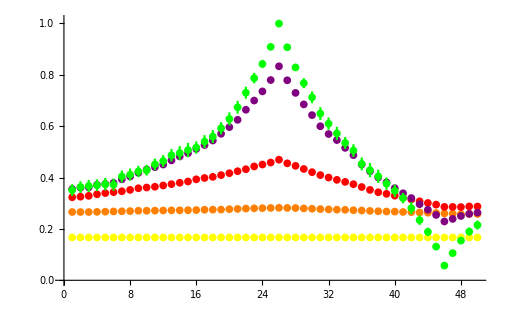

```mathematica
Show[
ErrorListPlot[Table[{DataMean[[1,2;;]][[i]],DataVar[[1,2;;]][[i]]},{i,1,50}],PlotRange->{0,1.01},PlotStyle->Yellow],
ErrorListPlot[Table[{DataMean[[5,2;;]][[i]],DataVar[[5,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Orange],
ErrorListPlot[Table[{DataMean[[10,2;;]][[i]],DataVar[[10,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Red],
ErrorListPlot[Table[{DataMean[[20,2;;]][[i]],DataVar[[20,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Purple],
ErrorListPlot[Table[{DataMean[[50,2;;]][[i]],DataVar[[50,2;;]][[i]]},{i,1,50}],PlotRange->{0,1},PlotStyle->Green]
]
```

## KJB model

Selection :

```mathematica
dpi=1/(1+s[i]p[i]+s[k]p[k])( s[i]p[i](1-p[i])+s[k]d[i,k])+p[i];
dpj=1/(1+s[i]p[i]+s[k]p[k])(s[i]d[i,j]+s[k]d[j,k])+p[j];
dpk=1/(1+s[i]p[i]+s[k]p[k])(s[k]p[k](1-p[k])+s[i]d[i,k])+p[k];
dij=1/(1+s[i]p[i]+s[k]p[k])(s[i](1-2p[i])d[i,j]+s[k]d[i,j,k])+d[i,j];
djk=1/(1+s[i]p[i]+s[k]p[k])(s[k](1-2p[k])d[j,k]+s[i]d[i,j,k])+d[j,k];
dik=1/(1+s[i]p[i]+s[k]p[k])(s[i]((1-2p[i])d[i,k])+s[k]((1-2p[k])d[i,k]))+d[i,k];
dijk=1/(1+s[i]p[i]+s[k]p[k])(s[i](p[i](1-p[i])d[j,k]+(1-2p[i])d[i,j,k])+s[k](p[k](1-p[k])d[i,j]+(1-2p[k])d[i,j,k]))+d[i,j,k];
```

Reference:

```mathematica
ddpi=dpi//Simplify;
ddpj=dpj//Simplify;
ddpk=dpk//Simplify;
ddij=dij-(p[i]-dpi)(p[j]-dpj)//Simplify;
ddjk=djk-(p[j]-dpj)(p[k]-dpk)//Simplify;
ddik=dik-(p[i]-dpi)(p[k]-dpk)//Simplify;
ddijk=dijk+dij(p[k]-dpk)+dik(p[j]-dpj)+djk(p[i]-dpi)-(p[i]-dpi)(p[j]-dpj)(p[k]-dpk)//Simplify;
```

Transmission:

```mathematica
dddpi=ddpi;
dddpj=ddpj;
dddpk=ddpk;
dddij=ddij(1-r[i,j]);
dddjk=ddjk(1-r[j,k]);
dddik=ddik(1-r[i,k]);
dddijk=ddijk(1-r[i,j])(1-r[j,k]);
```

```mathematica
Clear[Itterate3locus]
Itterate3locus[t_,p00_,si_,sk_,rij_,rjk_,rik_]:=Itterate3locus[t,p00,si,sk,rij,rjk,rik]=
Block[{p,d,i,r,j,k,s},
Itterate3locus[0,p00,si,sk,rij,rjk,rik]={p00,p00,p00,p00(1-p00),p00(1-p00),p00(1-p00),p00+2 p00^3-3 p00^2};
r[i,j]=rij;
r[j,k]=rjk;
r[i,k]=rik;
s[i]=si;
s[k]=sk;
p[i]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[1]];
p[j]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[2]];
p[k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[3]];
d[i,j]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[4]];
d[j,k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[5]];
d[i,k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[6]];
d[i,j,k]=Itterate3locus[t-1,p00,si,sk,rij,rjk,rik][[7]];

{dddpi,
dddpj,
dddpk,
dddij,
dddjk,
dddik,
dddijk}
];
```

```mathematica
Itterate3locus[5,0.5,0.1,-0.1,0.1,0.1,0.1]
```

{0.522633,0.5,0.477367,0.146923,0.146923,0.14635,-1.00936×10^-18}

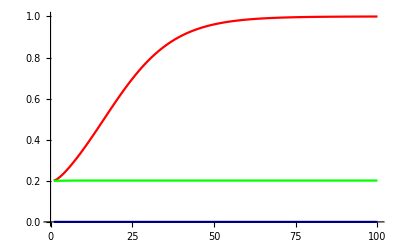

```mathematica
Show[
{ListLinePlot[Table[{t,Itterate3locus[t,0.2,0.1,-0.1,0.5,0.5,0.5][[1]]},{t,1,100}],PlotRange->{Automatic,{0,1}},PlotStyle->Red],
ListLinePlot[Table[{t,Itterate3locus[t,0.2,0.1,-0.1,0.5,0.5,0.5][[2]]},{t,1,100}],PlotRange->{Automatic,{0,1}},PlotStyle->Green],
ListLinePlot[Table[{t,Itterate3locus[t,0.,0.1,-0.1,0.5,0.5,0.5][[3]]},{t,1,100}],PlotRange->{Automatic,{0,1}},PlotStyle->Blue]}]
```

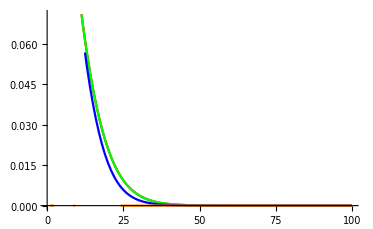

```mathematica
Show[
{ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[4]]},{t,1,100}],PlotStyle->Red],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[5]]},{t,1,100}],PlotStyle->Green],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[6]]},{t,1,100}],PlotStyle->Blue],
ListLinePlot[Table[{t,Itterate3locus[t,0.5,0.1,-0.1,0.1,0.1,0.1][[7]]},{t,1,100}],PlotStyle->Orange]}]
```

```mathematica
Pars={pi0->4/24,pj0->4/24,pk0->4/24,si->0.2,sk->-0.05};
```

```mathematica
Qinf[accuracy_,c_,R0_,p0_,s_]:=c R0(1-p0)Sum[(1-c)^n/(1-p0+p0(1+s)^(n+1)),{n,0,accuracy}];
```

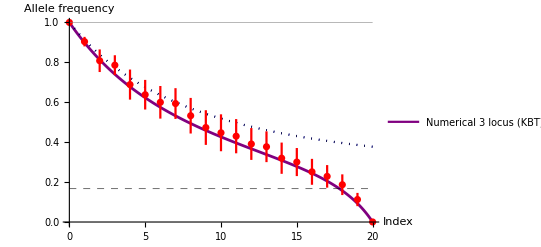

```mathematica
TotalDistance=20;
RecombRate=0.01;
Legended[Show[
ListLinePlot[Table[{nij,Itterate3locus[200,pi0/.Pars,si/.Pars,sk/.Pars,1-1/2 (1+(1-2 RecombRate)^nij),1-1/2 (1+(1-2 RecombRate)^(TotalDistance-nij)),1-1/2 (1+(1-2 RecombRate)^TotalDistance)][[2]]},{nij,0,TotalDistance,0.1}],PlotRange->{Automatic,{0,1}},PlotStyle->{Purple,Thickness[0.005]},AxesLabel->{"Index","Allele frequency"}],
ListLinePlot[Table[{nij,Itterate2locus[200,pi0/.Pars,si/.Pars,0,1-1/2 (1+(1-2 RecombRate)^nij)][[2]]},{nij,0,TotalDistance,0.1}],PlotRange->All,PlotStyle->{Blue,Dotted}],
ListLinePlot[Table[{nij,1-Qinf[1000,1-1/2 (1+(1-2 RecombRate)^nij),1,pi0/.Pars,si/.Pars]},{nij,0,TotalDistance,0.1}],PlotStyle->{Dotted,Black}],
ErrorListPlot[Table[{i-1,DataMean[[200,27;;47]][[i]],DataVar[[200,27;;47]][[i]]},{i,1,21}],PlotRange->{0,1},PlotStyle->Red],

ListLinePlot[Table[{nij,pi0/.Pars},{nij,0,TotalDistance}],PlotStyle->{Thickness[0.001],Dashed,Black}],

ListLinePlot[Table[{nij,1/.Pars},{nij,0,TotalDistance}],PlotStyle->{Thickness[0.001],Gray}]

],
LineLegend[{Purple},{"Numerical 3 locus (KBT)"}]
]
```

```mathematica
Export["/home/freek/Introgression/Example/Temp.pdf",%]
```

/home/freek/Introgression/Example/Temp.pdf

# SF Model

## Analytical solution

Assuming exponential growth of the invader and resident assumes that the populations remain small. When populations are larger, density dependence should be taken into account.

```mathematica
Pars={rRes->Log[1],rInv->Log[1],kRes->100,kInv->200,Θ->0};
```

```mathematica
nRes[t_]:=kRes*Exp[(t)*rRes];
nInv[t_]:=kInv*Exp[(t)*rInv];
```

```mathematica
Clear[simulatefrac]
simulatefrac[t_,rRes_,rInv_,kRes_,kInv_,Θ_]:=simulatefrac[t,rRes,rInv,kRes,kInv,Θ]=
Block[{
fracRes=simulatefrac[t-1,rRes,rInv,kRes,kInv,Θ][[1]],
fracInv=simulatefrac[t-1,rRes,rInv,kRes,kInv,Θ][[2]]},
nRes[t]=kRes*Exp[(t)*rRes];
nInv[t]=kInv*Exp[(t)*rInv];
newfracRes=(1/2*fracRes+1/2*fracInv)*nInv[t]/(nInv[t]+nRes[t])+(fracRes)*nRes[t]/(nInv[t]+nRes[t]);(*This is the equation describing how the genomic background changes for an individual carrying A, depending on who it mates with.*)
newfracInv=(1/2*fracRes+1/2*fracInv)*nRes[t]/(nInv[t]+nRes[t])+(fracInv)*nInv[t]/(nInv[t]+nRes[t]);
(*This is the equation describing how the genomic background changes for an individual carrying a, depending on who it mates with.*)

{newfracRes,newfracInv,nInv[t-1]/(nInv[t-1]+nRes[t-1]),nRes[t-1]/(nInv[t-1]+nRes[t-1])} 
]
simulatefrac[0,rRes/.Pars,rInv/.Pars,kRes/.Pars,kInv/.Pars,Θ/.Pars]={1,0,kInv/(kInv+kRes)/.Pars,kRes/(kInv+kRes)/.Pars};
```

#### JMS approximation for s=0

```mathematica
Qinf[accuracy_,c_,R0_,p0_,s_]:=c R0(1-p0)Sum[(1-c)^n/(1-p0+p0(1+s)^(n+1)),{n,0,accuracy}]
c R0(1-p0)Sum[(1-c)^n/(1-p0+p0(1+s)^(n+1))/.s->0,{n,0,Infinity}]/.R0->1
```

1-p0

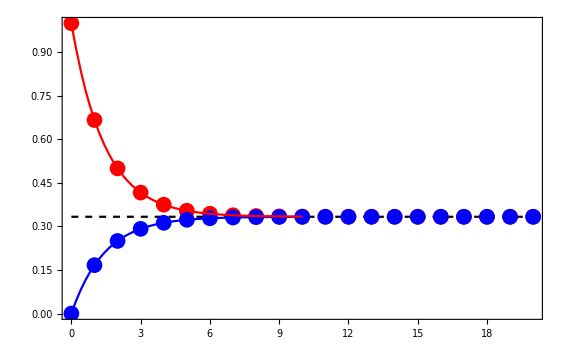

```mathematica
Show[
ListPlot[Table[{t,simulatefrac[t,rRes/.Pars,rInv/.Pars,kRes/.Pars,kInv/.Pars,Θ/.Pars][[1]]},{t,0,20}],PlotStyle->{PointSize[0.02],Red},PlotRange->{{0,20},{0,1}}],
ListPlot[Table[{t,simulatefrac[t,rRes/.Pars,rInv/.Pars,kRes/.Pars,kInv/.Pars,Θ/.Pars][[2]]},{t,0,20}],PlotStyle->{PointSize[0.02],Blue},PlotRange->{{0,20},{0,1}}],
ListLinePlot[Table[{t,1-kInv/(kInv+kRes)/.Pars},{t,0,20}],PlotStyle->{Black,Dashed}],
Plot[(-1+2^-n) (-1+p0)/.p0->kInv/(kInv+kRes)/.Pars,{n,0,10},PlotRange->All,PlotStyle->Blue],
Plot[1+(-1+2^-n) p0/.p0->kInv/(kInv+kRes)/.Pars,{n,0,10},PlotRange->All,PlotStyle->Red],
Frame->True
]
```

#### Similarities between JMS & SF

```mathematica
kI1=kI Exp[rI];
kR1=kR Exp[rR];
```

```mathematica
Solve[kI1/(kI1+kR1)==kI/(kI+kR)(1+s)/(1+(kI/(kI+kR))s),s]//FullSimplify
```

{{s→-1+ⅇ^(rI-rR)}}

```mathematica
Pars={rRes->Log[0.8],rInv->Log[1.2],kRes->1000,kInv->200,Θ->0};
simulatefrac[0,rRes/.Pars,rInv/.Pars,kRes/.Pars,kInv/.Pars,Θ/.Pars]={1,0,kInv/(kInv+kRes)/.Pars,kRes/(kInv+kRes)/.Pars};
Clear[Q]
Q[n_,p0_,s_]:=Q[n-1,p0,s]+(1/2 1(1-p0)(1-1/2)^(n-1))/(1-p0+p0(1+s)^n)
Q[0,kInv/(kInv+kRes)/.Pars,-1+ⅇ^(rInv-rRes)/.Pars]=0;
```

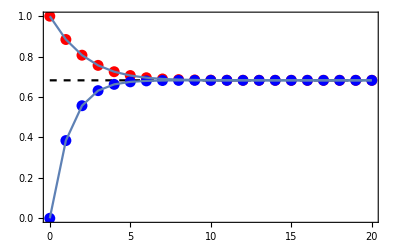

```mathematica
Show[
ListPlot[Table[{t,simulatefrac[t,rRes/.Pars,rInv/.Pars,kRes/.Pars,kInv/.Pars,Θ/.Pars][[1]]},{t,0,20}],PlotStyle->{PointSize[0.02],Red},PlotRange->{{0,20},{0,1}}],
ListPlot[Table[{t,simulatefrac[t,rRes/.Pars,rInv/.Pars,kRes/.Pars,kInv/.Pars,Θ/.Pars][[2]]},{t,0,20}],PlotStyle->{PointSize[0.02],Blue},PlotRange->{{0,20},{0,1}}],
ListLinePlot[Table[{t,Qinf[100,0.5,1,kInv/(kInv+kRes)/.Pars,-1+ⅇ^(rInv-rRes)/.Pars]},{t,0,20}],PlotStyle->{Black,Dashed}],
ListLinePlot[Table[{t,Q[t,kInv/(kInv+kRes)/.Pars,-1+ⅇ^(rInv-rRes)/.Pars]},{t,0,20}]],
ListLinePlot[Table[{t,(1-1/2)^t+Q[t,kInv/(kInv+kRes)/.Pars,-1+ⅇ^(rInv-rRes)/.Pars]},{t,0,20}],PlotRange->All],
Frame->True
]
```

```mathematica
Jhon Maynard Smith
```

Jhon Maynard Smith

```mathematica
Clear[Q,R]
Q[n_]:=Q[n-1]+c(1-p0)(1-c)^(n-1)/(1-p0+p0(1+s)^n);
R[n_]:=R[n-1]-((1-c)^(n-1) c p0 (1+s)^n)/(1+p0 (-1+(1+s)^(n-1)+s (1+s)^(n-1)));
Q[0]=0;
R[0]=1;
```

```mathematica
Q[100]/.p0->0.5/.c->0.2/.s->0.1
R[100]/.p0->0.5/.c->0.2/.s->0.1
```

0.389303

0.389303

```mathematica
Sally and Freek
```

and Freek Sally

```mathematica
Clear[nRes,nInv,fracRes,fracInv]
```

```mathematica
Pars
```

{rRes→-0.223144,rInv→0.182322,kRes→1000,kInv→200,Θ→0}

```mathematica
fracInv[n_]:=(1/2*fracRes[n-1]+1/2*fracInv[n-1])*(kRes*Exp[(n)*rRes])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])+(fracInv[n-1])*(kInv*Exp[(n)*rInv])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])/.Pars;
fracRes[n_]:=(1/2*fracRes[n-1]+1/2*fracInv[n-1])*(kInv*Exp[(n)*rInv])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])+(fracRes[n-1])*(kRes*Exp[(n)*rRes])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])/.Pars;
fracInv[0]=0;
fracRes[1]=1;
```

Uncouple these equations: Q[n]-R[n]=-(R0(1-c))^n where fracInv[n]=Q[n] and fracRes[n] = R[n]

```mathematica
Clear[fracInv,fracRes]
subme=Solve[{ave[t]==(fracInv[t]+fracRes[t])/2,dif[t]==fracRes[t]-fracInv[t]},{fracInv[t],fracRes[t]}][[1]];
```

```mathematica
fracResprime= (1/2*fracRes[t]+1/2*fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracRes[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes]);
fracInvprime=(1/2*fracRes[t]+1/2*fracInv[t])*(kRes*Exp[t*rRes])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes])+(fracInv[t])*(kInv*Exp[t*rInv])/(kInv*Exp[t*rInv]+kRes*Exp[t*rRes]);
difprime=fracResprime-fracInvprime/.subme//Simplify
```

dif[t]/2

```mathematica
RSolve[{dif[t+1]==dif[t]/2,dif[0]==1},dif[t],t]
```

{{dif[t]→2^-t}}

fracRes[t]-fracInv[t]=2^-t

```mathematica
Clear[nRes,nInv,fracRes,fracInv]
fracInv[n_]:=fracInv[n]=(1/2*(2^(-(n-1))+fracInv[n-1])+1/2*fracInv[n-1])*(kRes*Exp[(n)*rRes])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])+(fracInv[n-1])*(kInv*Exp[(n)*rInv])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])/.Pars;
fracRes[n_]:=fracRes[n]=(1/2*fracRes[n-1]+1/2*(fracRes[n-1]-2^(-(n-1))))*(kInv*Exp[(n)*rInv])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])+(fracRes[n-1])*(kRes*Exp[(n)*rRes])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])/.Pars;
fracInv[0]=0;
fracRes[0]=1;
```

```mathematica
fracInv[20]
fracRes[20]
```

0.682635

0.682636

```mathematica
Clear[fracInv,fracRes]
(1/2*(2^(-(n-1))+fracInv[n-1])+1/2*fracInv[n-1])*(kRes*Exp[(n)*rRes])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])+(fracInv[n-1])*(kInv*Exp[(n)*rInv])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])//FullSimplify
(1/2*fracRes[n-1]+1/2*(fracRes[n-1]-2^(-(n-1))))*(kInv*Exp[(n)*rInv])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])+(fracRes[n-1])*(kRes*Exp[(n)*rRes])/(kInv*Exp[(n)*rInv]+kRes*Exp[(n)*rRes])//FullSimplify
```

(2^-n kRes)/(ⅇ^(n (rInv-rRes)) kInv+kRes)+fracInv[-1+n]

-(2^-n kInv)/(kInv+ⅇ^(n (-rInv+rRes)) kRes)+fracRes[-1+n]

```mathematica
Same when
```

Same when

```mathematica
c(1-p0)(1-c)^(n-1)/(1-p0+p0(1+s)^n)/.c->1/2/.p0->kInv/(kInv+kRes)//FullSimplify
```

(2^-n kRes)/(kRes+kInv (1+s)^n)

```mathematica
Solve[(2^-n kRes)/(ⅇ^(n (rInv-rRes)) kInv+kRes)==(2^-n kRes)/(kRes+kInv (1+s)^n),s]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→-1+(ⅇ^(n (rInv-rRes)))^(1/n)}}

```mathematica
sel=-1+ⅇ^(rInv-rRes)
```

-1+ⅇ^(rInv-rRes)

```mathematica
Clear[s]
```

```mathematica
kI1=kI Exp[rI];
kR1=kR Exp[rR];
Solve[kI1/(kI1+kR1)==kI/(kI+kR)(1+s)/(1+(kI/(kI+kR))s),s]//FullSimplify
```

{{s→-1+ⅇ^(rI-rR)}}

#### Solution

```mathematica
Qinf=(1/2)(1-p0)Sum[(1/2)^n/(1-p0+p0(1+s)^(n+1)),{n,0,Infinity}]//FullSimplify
```

-1/2 (-1+p0) ∑_(n=0)^∞ 2^-n/(1-p0+p0 (1+s)^(1+n))

## Truncated deterministic rescue

```mathematica
nRescrit=5;
Pars={rRes->-0.2,rInv->0.18,kRes->1000,kInv->5};
```

```mathematica
Q[n_,s_,kRes_,kInv_]:=Sum[(2^(-1-t) kRes)/(kRes+kInv (1+s)^(1+t)),{t,0,n-1}]//Simplify
```

```mathematica
nRes[t_]:=nRes0*Exp[(t)*rRes];
```

```mathematica
tcrit[rRes_,kRes_]:=Floor[1/rRes Log[nRescrit/kRes]];
```

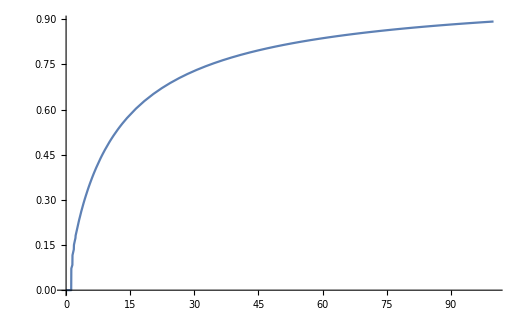

```mathematica
Plot[Q[tcrit[rRes/.Pars,kRes],-1+ⅇ^(rInv-rRes)/.Pars,kRes,kInv/.Pars],{kRes,0,100},PlotRange->All]
```

## Fixation probability

```mathematica
{1-P==Sum[PDF[PoissonDistribution[1+s],j](1-P)^j,{j,0,Infinity}]}
```

{1-P==ⅇ^(-P (1+s))}

```mathematica
Normal[Series[1-P-ⅇ^(-P (1+s))/.P->P ϵ/.s->s ϵ,{ϵ,0,2}]]
```

(-P^2/2+P s) ϵ^2

```mathematica
Solve[%==0,P]
```

{{P→0},{P→2 s}}

```mathematica
2(-1+ⅇ^(rI-rR))/.rI->Log[1+sI]/.rR->Log[1+sR]
```

2 (-1+(1+sI)/(1+sR))

```mathematica
2 (-1+(1+sI)/(1+sR))/.sI->0.01/.sR->0
```

0.02

```mathematica
Factor[Normal[Series[1-P[k]-ⅇ^(-P[1] k (1+s))/.P[1]->2 s/.P[k]->P[k] ϵ/.s->s ϵ,{ϵ,0,1}]]]
```

ϵ (2 k s-P[k])

```mathematica
Solve[%==0,P[k]]//Simplify
```

{{P[k]→2 k s}}

## PDF of waiting time until extinction

```mathematica
Clear[Ce,g]
```

```mathematica
Ce[n_,i_,k_]:=Product[(n-j)μ,{j,0,i-1}]/Product[If[j≠ k,(k-j)μ,1],{j,0,n-1}]
```

```mathematica
g[n_,t_,μ_]:=μ Sum[Ce[n,n-1,k]Exp[-μ(n-k)t],{k,0,n-1}]
```

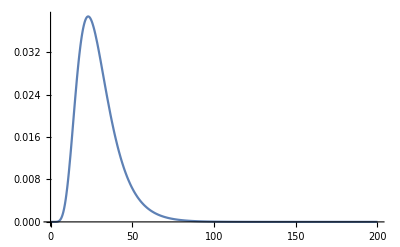

```mathematica
Plot[g[10,t,0.1],{t,0,200},PlotRange->All]
```

```mathematica
nRes[t_]:=10*Exp[(t)*Log[1-μ]];
```

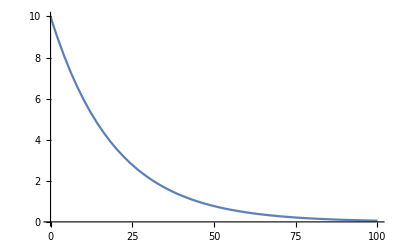

```mathematica
Plot[nRes[t]/.μ->0.05,{t,0,100}]
```

```mathematica
Q[n_]:=Sum[(2^(-1-t) kRes)/(kRes+kInv (1+s)^(1+t)),{t,0,n-1}]//Simplify
```

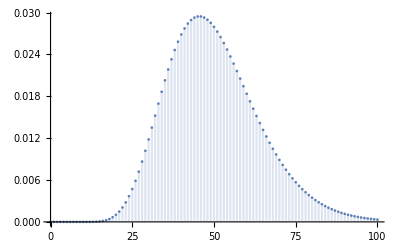

```mathematica
DiscretePlot[Binomial[k-1,r-1] p^r(1-p)^(k-r)/.r->10/.p->0.2,{k,0,100}]
```

```mathematica
Sum[Binomial[r-1,k-1] p^r(1-p)^(k-r),{k,0,Infinity}]//FullSimplify
```

(1+1/(-2+p))^(1-r) p^r

```mathematica
PDF[NegativeBinomialDistribution[n,p],k]
```

Piecewise[{{(1-p)^k p^n Binomial[-1+k+n,-1+n], k≥0}, {0, True}}]

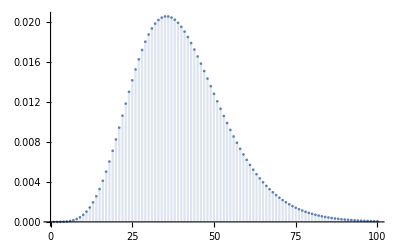

```mathematica
DiscretePlot[((1-p)^k p^n Binomial[-1+k+n,-1+n])(Sum[(2^(-1-t) n)/(n+(1+1)^(1+t)),{t,0,k-1}])/.p->0.2/.n->10,{k,0,100}]
```

```mathematica
Sum[((1-p)^k p^n Binomial[-1+k+n,-1+n])(Sum[(2^(-1-t) n)/(n+(1+1)^(1+t)),{t,0,k-1}])/.p->0.2/.n->10,{k,0,200}]
```

```mathematica
RSolve[{P[t+1]==-mu P[t],P[0]==P0},P[t],t]//FullSimplify
```

{{P[t]→(-mu)^t P0}}

```mathematica
RSolve[{P[t+1]==mu
```

```mathematica
Manipulate[DiscretePlot[(1-p)p^(n-1),{n,0,100},PlotRange->All],{p,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Power::indet: Indeterminate expression 0^0 encountered.

```mathematica
PN1=μN(-μN)^0 PN0-μN1PN10;
PN2-
```

```mathematica
Sum[n,{n,1,1}]
```

1

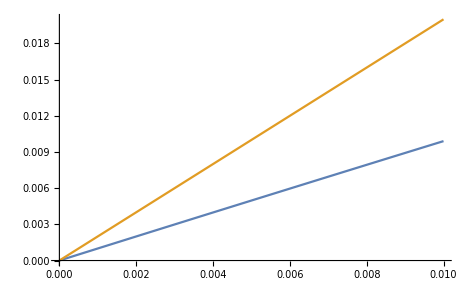

```mathematica
Plot[{1-1/(1+s),2s},{s,0,0.01}]
```

```mathematica
T1=d1 T0+(1-b1-d1)T1+b1 T2+1
T2=d2 T1+(1-b2-d2)T2+b2 T3+1
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of d1 T0.

Hold[1+d1 T0+(1-b1-d1) T1+b1 T2]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of d1 T0.

Hold[T2=d2 T1+(1-b2-d2) T2+b2 T3+1]

```mathematica
p
```

```mathematica
Clear[T1]
```

```mathematica
d2 T1+(1-b2-d2)T2+b2 T3+1-(d1 T0+(1-b1-d1)T1+b1 T2+1)//FullSimplify
```

(-1+b1+d2) T1+d1 (-T0+T1)+T2-(b1+b2+d2) T2+b2 T3

```mathematica
T[i_,m_,b_,d_]:=Sum[(d/b)^k,{k,0,i-1}]/Sum[(d/b)^k,{k,0,m-1}] Sum[Sum[(b/d)^k/(b j(b/d)^k),{j,1,k}],{k,1,m-1}]-Sum[Sum[(b/d)^k/(b j(b/d)^k),{j,1,k}],{k,1,i-1}]
```

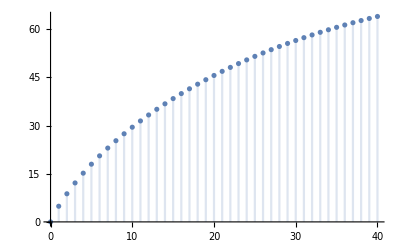

```mathematica
DiscretePlot[T[i,200,1,1],{i,0,40}]
```